## Initial Setup

```mathematica
SetDirectory["~/myWork/np_sandbox/008"]
```

/Users/npadmana/myWork/np_sandbox/008

## Data

Read in the data, into data sets origP and origQ, and plot these to get a sense of the layout.

```mathematica
origP= Import["image.dat", "Table"];
```

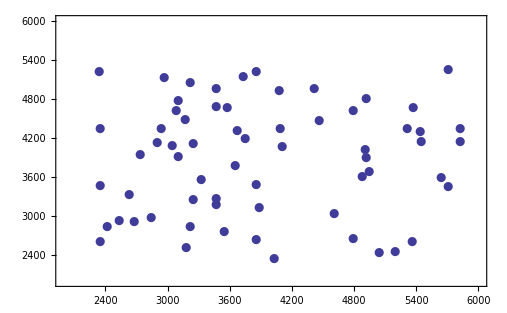

```mathematica
ListPlot[origP, Frame->True, PlotMarkers->{Automatic, 12}, PlotRange->{{2000,6000},{2000,6000}}]
```

```mathematica
origQ = Import["specified.dat","Table"];
```

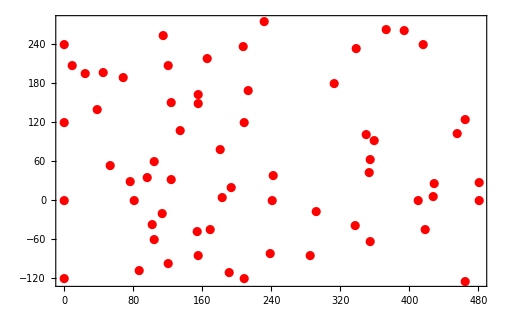

```mathematica
ListPlot[origQ, Frame->True, PlotMarkers->{Automatic, 12}, PlotRange->Automatic, Axes->False, PlotStyle->Red]
```